```mathematica
myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.005;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=12;
cm=72/2.54;

ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};

SetOptions[MatrixPlot,FrameTicksStyle->Black,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],ImageSize->imagSize,AspectRatio->1];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListDensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}}];
SetOptions[DensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];

SetOptions[ListLogLogPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];


fTXT[txt_]:=Text[Style[txt,FontFamily->font,FontSize->fontSize]]
itTXT[txt_]:=Text[Style[txt,FontFamily->font,FontSize->fontSize,FontColor->Black,FontSlant->Italic]]
sTXT[txt_,size_]:=Text[Style[txt,FontFamily->font,FontSize->size]]

getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];
BorderDimensions[im]]


(*Needs["PacletManager`"]*)
(*PacletInstall[NotebookDirectory[]<>"/MaTeX-1.7.4.paclet"]*)
<<MaTeX`
new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
ColorData["GoogleGradient"]
new={{"GoogleGradientRev","",{}},{"Gradients"},1,{0,1},Reverse[{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred}],""};
ColorData["GoogleGradientRev"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
ColorData["GoogleGradientRev"]
new={{"GoogleGradientBlue","",{}},{"Gradients"},1,{0,1},{Darker[myblue],Lighter[myblue,.5],Lighter[myblue,.75],White},""};
ColorData["GoogleGradientBlue"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
ColorData["GoogleGradientBlue"]
new={{"GoogleGradientGray","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],Lighter[mygray,.8],Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradientGray"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
ColorData["GoogleGradientGray"]
<<MaTeX`
new={{"WhiteBlack","",{}},{"Gradients"},1,{0,1},Reverse[{White,Lighter[Black,.99],Lighter[Black,.98],Lighter[Black,.97],Lighter[Black,.96],Lighter[Black,.95],Black}],""};
ColorData["WhiteBlack"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
ColorData["WhiteBlack"]
new={{"YellowRedBlack","",{}},{"Gradients"},1,{0,1},Reverse[{Blend[{myyellow,White},.95],Blend[{myred,myyellow},.85],Blend[{myred,myyellow},.85],Blend[{Black,myred},.75],Black}],""};
ColorData["YellowRedBlack"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
ColorData["YellowRedBlack"]

SetOptions[MaTeX,"Preamble"->{"\\usepackage[rgb,dvipsnames]{xcolor}","\\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373}","\\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392}","\\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882}","\\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}",
"\\AtBeginDocument{\\color{white}}"}]
```

ColorDataFunction[…]

ColorDataFunction[…]

ColorDataFunction[…]

«3 more identical outputs»

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage[rgb,dvipsnames]{xcolor},\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373},\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392},\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882},\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588},\AtBeginDocument{\color{white}}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

## Dispersion and Eigenstates in the thermodynamic limit

```mathematica
Clear[eps,blochH,eval,evec]
eps[k_,J_,Jpr_]:=Sqrt[J^2+Jpr^2+2J*Jpr*Cos[k]]
blochH[k_,J_,Jpr_,mu_]:={{mu, J+Jpr*ⅇ^(ⅈ*k)},{J*+Jpr**ⅇ^(-ⅈ*k),-mu}}
{eval[k_,J_,Jpr_,mu_],evec[k_,J_,Jpr_,mu_]}=Eigensystem[blochH[k,J,Jpr,mu]];
```

```mathematica
Manipulate[Plot[Normalize[evec[k,j,jpr,1.][[1]]]//Abs,{k,-π,π}],{j,0,2},{jpr,1,2}]
```

```mathematica
tns=Thickness[.015];

j=1.;
jpr=0.;
Clear[j,jpr,inset]

pts=ts;
ts=244/114*ts;
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-0.5"],ts},{-2,MaTeX["-1"],ts},{-3,MaTeX["-1.5"],ts},{+1,MaTeX["+0.5"],ts},{+2,MaTeX[""],ts},{+3,MaTeX[""],ts},{+2.4,Rotate[MaTeX["\\tilde\\epsilon_\\pm(k)"],π/2],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0.,MaTeX["0
"],ts},{-1,MaTeX["-1"],ts},{1,MaTeX[""],ts},{-.5,MaTeX[""],ts},{.5,MaTeX[""],ts}},{{.85,MaTeX["k/\\pi"],.0}}],{None}}}; 
ts=pts; 
export[j_,jpr_,dt_]:=Module[{},
inset="J'/J="<>ToString[NumberForm[(jpr-dt)/(j+dt),{4,2}]];
plt=Plot[Evaluate[2{-1,+1}*eps[k*π,j+dt,jpr-dt]/(j+jpr)],{k,-1,+1},GridLines->None,Background->None,FrameStyle->Black,FrameTicks->ticks,FrameTicksStyle->Black,PlotStyle->{Directive[Black,tns],Directive[Black,tns]},PlotRange->{-3,3},Epilog->Inset[MaTeX[inset],{0,2.6}],ImageSize->{Automatic,156},AspectRatio->GoldenRatio,ImagePadding->{{30,2},{21,2}}];
fn=inset;
fn=StringReplace[fn,"/"->"div"];
Export["dispersion_"<>fn<>".png",plt,ImageResolution->600]
]
```

```mathematica
tns=Thickness[.015];

j=1.;
jpr=0.;
Clear[j,jpr,inset]

pts=ts;
ts=244/90*ts;
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-0.5"],ts},{-2,MaTeX["-1"],ts},{-3,MaTeX["-1.5"],ts},{+1,MaTeX["+0.5"],ts},{+2,MaTeX[""],ts},{+3,MaTeX[""],ts},{+2.4,Rotate[MaTeX["\\tilde\\epsilon_\\pm(k)"],π/2],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0.,MaTeX["0
"],ts},{-1,MaTeX["-1"],ts},{1,MaTeX[""],ts},{-.5,MaTeX[""],ts},{.5,MaTeX[""],ts}},{{.85,MaTeX["k/\\pi"],.0}}],{None}}}; 
ts=pts; 
cexport[j_,jpr_,dt_]:=Module[{},
inset="J'/J="<>ToString[NumberForm[(jpr-dt)/(j+dt),{4,2}]];
plt=Plot[Evaluate[2{-1,+1}*eps[k*π,j+dt,jpr-dt]/(j+jpr)],{k,-1,+1},GridLines->None,Background->None,FrameStyle->Black,FrameTicks->ticks,FrameTicksStyle->Black,PlotStyle->{Directive[Black,tns],Directive[Black,tns]},PlotRange->{-3,3},Epilog->Inset[MaTeX[inset],{0,2.6}],ImageSize->{Automatic,156},AspectRatio->GoldenRatio,ImagePadding->{{6,2},{21,2}}];
fn=inset;
fn=StringReplace[fn,"/"->"div"];
Export["cropped_dispersion_"<>fn<>".png",plt,ImageResolution->1200]
]
```

$Aborted

```mathematica
ImageDimensions[plt]
```

{114,156}

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_white_pictures/vsdt"]
Do[
export[2.,0.,dt]
,{dt,{0,-0.5,-1,-1.5}}]
```

/Users/andreas/Desktop/talk_white_pictures/vsdt

## Open Boundaries

```mathematica
Clear[H,t,δt,t1,t2,i,pot,eval,Ug,diagonalizeSpinfulSSH]
diagonalizeSpinfulSSH[L_,pbc_,dt_,amp_,σx_,sb_]:=Module[{H,eval,pot,t1,Ug,order, δt,t},
pot[x_,sigmax_,x0_]:=PDF[NormalDistribution[x0,sigmax],x];
t1[i_]:=If[EvenQ[i],1.0,δt];
H=ConstantArray[0,{2*L,2*L}];
Do[
H[[2*i-1,2*i+1]]+=t1[i];
H[[2*i,2*i+2]]+=t1[i];
,{i,1,L-1}];
Do[
H[[2*i-1,2*i]]+=sb;
,{i,1,L}];
H = H + H†;
H = H/.{δt->dt,t->-1.0};
{eval,Ug}=Eigensystem[H];
order = Ordering[eval];
eval=eval[[order]];
Ug=Ug[[order]];
Table[Ug[[i]]=Normalize[Ug[[i]]],{i,Length[Ug]}];
{eval,Ug, H}];
```

```mathematica
exportobc[j_,exp_]:=Module[{plt},
L=16;  (* size of the system *)
enne=L;  (* Number of fermions *)
σx=0.; (* variance of the Gaussian potential *)
sb = 0.; (* local spin flip *)
amp=0.0 10^-4;
(*amp=0.0;*)
pbc=False;
tmax= 2L;
Δt=tmax/100;
dt=j;
qpos=L/2;
qspecies = 1;
{e0,U0, H0}=Chop[diagonalizeSpinfulSSH[L,pbc,dt,amp,σx,sb]]; 
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX[""],ts},{+3,MaTeX[""],ts},{+2.8,Rotate[MaTeX["\\epsilon_\\pm(\\#)"],π/2],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{1,MaTeX["1"],ts},{L,MaTeX["L"],ts},{L/2,MaTeX["L/2"],ts}}],{None}}};
inset="J="<>ToString[NumberForm[dt,{4,2}]]<>"\\quad J'="<>ToString[NumberForm[1.0,{4,2}]];
plt=ListPlot[{Reverse[e0[[;;L]]],e0[[L+1;;]]},PlotRange->{{0,L+1},{-3,3}},GridLines->None,ImagePadding->{{22.148917558594974,4.},{22.148917558594974,11.704963918619853}},Joined->False,PlotMarkers->{{"▼",Scaled[.075]},{"▲",Scaled[.075]}},Background->Black,FrameStyle->White,FrameTicks->ticks,FrameTicksStyle->White,PlotStyle->{Directive[White,tns],Directive[White,tns]},PlotRange->{-3,3},Epilog->Inset[MaTeX[inset],{L/2,2.6}]];
fn=inset;
fn=StringReplace[fn,"\\quad "->""];
If[exp==True,Export["dispersion_"<>fn<>".png",plt,ImageResolution->600];,plt]
]
```

```mathematica
gap={};
Do[
tp={};
Do[
{e0,U0, H0}=Chop[diagonalizeSpinfulSSH[L,pbc,dt,amp,σx,sb]]; 
AppendTo[tp,{dt,(e0[[L+1]]-e0[[L]])}]
,{dt,0.,2,.025}];
AppendTo[gap,tp];
,{L,{8,16,32,64,128,256}}]
```

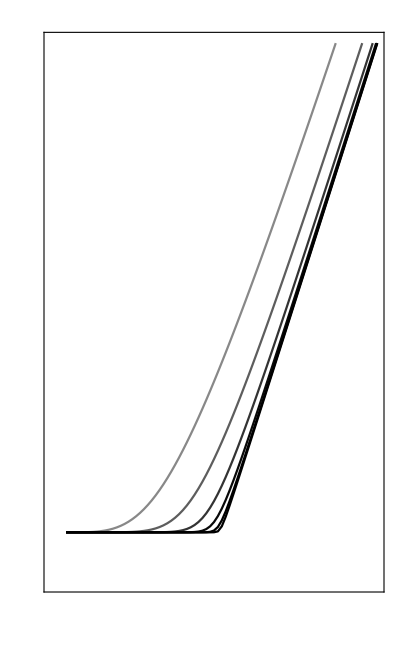

```mathematica
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX[""],ts},{+3,MaTeX[""],ts},{+1.8,MaTeX["\\tilde\\Delta"],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{1,MaTeX["1"],ts},{0,MaTeX["0"],ts},{2,"",ts},{1.9,MaTeX["J"],0ts}}],{None}}};
ListPlot[gap,PlotStyle->Table[{.9tns,Black,Opacity[.3+i/Length[gap]]},{i,Length[gap]}],FrameStyle->Black,FrameTicks->ticks,GridLines->None,FrameTicksStyle->Black,Background->None,PlotStyle->{Directive[Black,tns],Directive[Black,tns]},PlotRange->{{-.1,2.},2{-.1,1}},Epilog->Inset[MaTeX[inset],{L/2,2.6}],ImagePadding->{{30,2},{21,2}},ImageSize->{Automatic,156},AspectRatio->GoldenRatio]
```

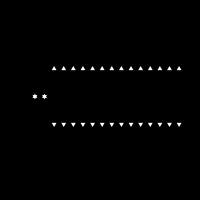

```mathematica
im=exportobc[.0,False]
```

```mathematica
<<GraphicsInformation`
BorderDimensions[im]
GraphicsInformation[im]
```

{{2,3},{3,3}}

{ImagePadding→{{22.1489,4.},{22.1489,11.705}},ImageSize→{200.,207.705},PlotRangeSize→{173.851,173.851},ImagePaddingSize→{26.1489,33.8539},PlotRange→{{0.,17.},{-3.,3.}},BasePlotRange→{{0.,17.},{-3.,3.}}}

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/obc_energy"]
Do[
exportobc[j,True];
,{j,0.,2.,0.025}]
```

/Users/andreas/Desktop/talk_black_pictures/obc_energy

```mathematica
exportobc2[num_,j_,exp_]:=Module[{plt},
L=32;  (* size of the system *)
enne=L;  (* Number of fermions *)
σx=0.; (* variance of the Gaussian potential *)
sb = 0.; (* local spin flip *)
amp=0.0 10^-4;
(*amp=0.0;*)
pbc=False;
tmax= 2L;
Δt=tmax/100;
dt=j;
qpos=L/2;
qspecies = 1;
{e0,U0, H0}=Chop[diagonalizeSpinfulSSH[L,pbc,dt,amp,σx,sb]];
ticks={{{{10^-16,Rotate[MaTeX["10^{-16}"],π/2],ts},{10^-8,Rotate[MaTeX["10^{-8}"],π/2],ts},{+1.0,Rotate[MaTeX["|\\psi^2(x)|"],π/2],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{1,MaTeX["1"],ts},{L,MaTeX["L"],ts},{L/2,MaTeX["L/2"],ts}}],{None}}};
inset="{\\color{mygreen}J="<>ToString[NumberForm[dt,{4,2}]]<>"}\\quad J'="<>ToString[NumberForm[1.0,{4,2}]];
plt=ListLogPlot[{Abs[U0[[L-num,;;;;2]]]^2+Abs[U0[[L-num,2;;;;2]]]^2,Abs[U0[[L-num+1,;;;;2]]]^2+Abs[U0[[L-num+1,2;;;;2]]]^2,Abs[U0[[L-num+2,;;;;2]]]^2+Abs[U0[[L-num+2,2;;;;2]]]^2,Abs[U0[[L-num+3,;;;;2]]]^2+Abs[U0[[L-num+3,2;;;;2]]]^2},PlotRange->{{-.05L,1.05*L},{10^-20,10}},GridLines->{{},{10^-2,10^-4,10^-8,10^-16}},PlotMarkers->{"●",Scaled[0.075]},Frame->True,Axes->False,GridLinesStyle->{Dashed,White},Background->Black,FrameStyle->White,FrameTicks->ticks,FrameTicksStyle->White,AspectRatio->1,PlotStyle->{Directive[White,tns],Directive[White,tns]},PlotRange->{-3,3},Epilog->Inset[MaTeX[inset],{L/2,10^-16}],ImagePadding->{{22.148917558594974,4.},{22.148917558594974,11.704963918619853}},ImageSize->imagSize];
fn=inset;
fn=StringReplace[fn,"\\quad "->""];
fn=StringReplace[fn,"{\\color{mygreen}"->""];
fn=StringReplace[fn,"}"->""];
If[exp==True,Export["localization_"<>fn<>".png",plt,ImageResolution->600];,plt]
]
```

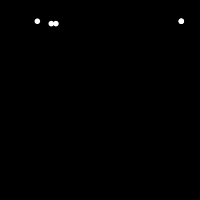

```mathematica
exportobc2[0,0,False]
```

```mathematica
U0[[L]]//Abs
```

{0,0.039254,0,0,0,0.0039254,0,0,0,0.00039254,0,0,0,0.000039254,0,0,0,3.9254×10^-6,0,0,0,3.9254×10^-7,0,0,0,3.9254×10^-8,0,9.94213×10^-10,0,3.9254×10^-9,0,9.94213×10^-9,0,3.9254×10^-10,0,9.94213×10^-8,0,0,0,9.94213×10^-7,0,0,0,9.94213×10^-6,0,0,0,0.0000994213,0,0,0,0.000994213,0,0,0,0.00994213,0,0,0,0.0994213,0,0,0,0.994213}

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/obc_localization"]
Do[
exportobc2[1,j,True];
,{j,0.,2.,0.025}]
```

/Users/andreas/Desktop/talk_black_pictures/obc_localization

```mathematica
L=256;  (* size of the system *)
enne=L;  (* Number of fermions *)
σx=0.; (* variance of the Gaussian potential *)
sb = 0.; (* local spin flip *)
amp=0.0 10^-4;
(*amp=0.0;*)
pbc=False;
tmax= 2L;
Δt=tmax/100;
qpos=L/2;
qspecies = 1;
spectrum={};
Monitor[
Do[
{e0,U0, H0}=Chop[diagonalizeSpinfulSSH[L,pbc,dt,amp,σx,sb]];
AppendTo[spectrum,e0];
,{dt,0,2,0.025}];
,dt]
```

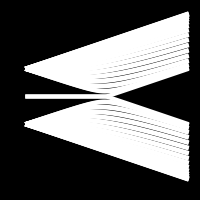

```mathematica
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX[""],ts},{+3,MaTeX[""],ts},{+2.8,Rotate[MaTeX["\\epsilon_\\pm"],π/2],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{1,MaTeX["1"],ts},{0,MaTeX["0"],ts},{2,"",ts},{1.9,MaTeX["J"],0ts}}],{None}}};
plt=ListPlot[Join[spectrumᵀ[[;;;;L/16]],spectrumᵀ[[L/16;;;;L/16]]],DataRange->{0,2},Frame->True,Axes->False,GridLines->None,Background->Black,FrameStyle->White,FrameTicks->ticks,FrameTicksStyle->White,AspectRatio->1,PlotStyle->{Directive[White,tns],Directive[White,tns]},PlotRange->{-3,3},Epilog->Inset[MaTeX[inset],{L/2,10^-16}],ImagePadding->{{22.148917558594974,4.},{22.148917558594974,11.704963918619853}},ImageSize->imagSize]
```

```mathematica
Table[Length[Select[Abs[sp],#<10^-4&]]/2,{sp,spectrum}]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

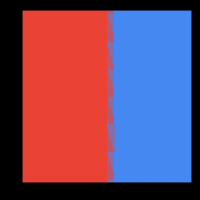

```mathematica
Show[ListDensityPlot[Partition[Flatten[Table[{j,e,If[j<1.05,-1,0]},{j,-.1,2.1,.1},{e,-4,4}]],3],Frame->True,Axes->False,GridLines->None,PlotRangePadding->0,PlotRange->{{-0.04166666666666667,2.0416666666666665},{-3.,3.}},Background->Black,FrameStyle->White,FrameTicks->ticks,FrameTicksStyle->White,AspectRatio->1,ColorFunction->"GoogleGradientRev",Epilog->Inset[MaTeX[inset],{L/2,10^-16}],ImagePadding->{{22.148917558594974,4.},{22.148917558594974,11.704963918619853}},ImageSize->imagSize],PlotRange->{{-0.04166666666666667,2.0416666666666665},{-3.,3.}}]
```

```mathematica
<<GraphicsInformation`
BorderDimensions[plt]
GraphicsInformation[plt]
```

{{2,3},{5,11}}

{ImagePadding→{{22.1489,4.},{22.1489,11.705}},ImageSize→{200.,207.705},PlotRangeSize→{173.851,173.851},ImagePaddingSize→{26.1489,33.8539},PlotRange→{{-0.0416667,2.04167},{-3.,3.}},BasePlotRange→{{0.,2.},{-3.,3.}}}

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/spectrum"]
Do[
inset="J="<>ToString[NumberForm[jay,{4,2}]]<>"\\quad J'="<>ToString[NumberForm[1.0,{4,2}]];
fn=inset;
fn=StringReplace[fn,"\\quad "->""];
tp=Show[plt,GridLines->{{jay},{}},GridLinesStyle->{mygreen,Dashed}];
Export["spectrum_"<>fn<>".png",tp,ImageResolution->600];
,{jay,0,2,0.025}]
```

/Users/andreas/Desktop/talk_black_pictures/spectrum

```mathematica
d[j_,jpr_,k_]:={Re[j]+Abs[jpr]*Cos[k+Arg[jpr]],Im[j]+Abs[jpr]*Sin[k+Arg[jpr]],0}
ed[j_,jpr_,k_]:=d[j,jpr,k]/Norm[d[j,jpr,k]]
```

```mathematica
dpr[t_,k_] := {(1-t)+t Cos[k],t Sin[k],Sin[π t]}
edpr[t_,k_]:=dpr[t,k]/Norm[dpr[t,k]]
```

```mathematica
PauliMatrix[1]*(J+Jpr Cos[k])-PauliMatrix[2]*(Jpr Sin[k])//FullSimplify//MatrixForm
```

(0 | J+ⅇ^(ⅈ k) Jpr
J+ⅇ^(-ⅈ k) Jpr | 0)

```mathematica
Clear[exportwinding1]
exportwinding1[j_,jpr_,exp_]:=Module[{plt},
jay=j;
jaypr=jpr;
jv = 2{jay,jaypr};
ahs=.075;
ath=.015;

pts=ts;
ts=244/114*ts;
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX[""],ts},{+3,MaTeX[""],ts},{+1.8,MaTeX["d_y"],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{-1,MaTeX[""],ts},{1,MaTeX["1"],ts},{0,MaTeX["0"],ts},{2,MaTeX["2"],ts},{-2,"",ts},{3,"",ts},{2.8,MaTeX["d_x"],0ts}}],{None}}};
ts=pts;
inset1="J="<>ToString[NumberForm[jay,{4,2}]];
inset2="J'="<>ToString[NumberForm[jaypr,{4,2}]];
plt=Show[
ParametricPlot[d[jay,jaypr,k*π][[;;2]],{k,-1,1},
PlotRange->{{-1,3},2{-1,1}},GridLines->{{0},{0}},Frame->True,Axes->False,GridLinesStyle->{{Dotted,Black},{Dotted,Black}},Background->None,FrameStyle->Black,FrameTicks->ticks,FrameTicksStyle->Black,AspectRatio->GoldenRatio,PlotStyle->{Directive[Black,tns],Directive[Black,tns]},PlotRange->{-3,3},ImageSize->{Automatic,156},AspectRatio->GoldenRatio,ImagePadding->{{30,2},{21,2}}
],
Graphics[Table[{Arrowheads[Min[Norm[jv],1]ahs],Blend[{mygreen,Black},0.5*k],Thickness[Min[Norm[jv],1]ath],Arrow[(jv={{0,0},d[jay,jaypr,k*2π][[;;2]]})]},{k,1,0,-.05}]],
ParametricPlot[d[jay,jaypr,k*π][[;;2]],{k,-1,1},
PlotRange->{{-1,3},2{-1,1}},GridLines->{{0},{0}},Frame->True,Axes->False,GridLinesStyle->{{Dotted,Black},{Dotted,Black}},Background->None,FrameStyle->Black,FrameTicks->ticks,FrameTicksStyle->Black,AspectRatio->GoldenRatio,PlotStyle->{Directive[Black,tns],Directive[Black,tns]},PlotRange->{-3,3},ImageSize->{Automatic,156},AspectRatio->GoldenRatio,ImagePadding->{{6,2},{21,2}}
],
Epilog->{Inset[MaTeX[inset1],{1,1.7}],Inset[MaTeX[inset2],{1,-1.7}]}
];
(*ListLogPlot[{Abs[U0[[L-num,;;;;2]]]^2+Abs[U0[[L-num,2;;;;2]]]^2,Abs[U0[[L-num+1,;;;;2]]]^2+Abs[U0[[L-num+1,2;;;;2]]]^2,Abs[U0[[L-num+2,;;;;2]]]^2+Abs[U0[[L-num+2,2;;;;2]]]^2,Abs[U0[[L-num+3,;;;;2]]]^2+Abs[U0[[L-num+3,2;;;;2]]]^2},PlotRange->{{-.05L,1.05*L},{10^-20,10}},GridLines->{{},{10^-2,10^-4,10^-8,10^-16}},PlotMarkers->{"●",Scaled[0.075]},Frame->True,Axes->False,GridLinesStyle->{Dashed,White},Background->Black,FrameStyle->White,FrameTicks->ticks,FrameTicksStyle->White,AspectRatio->1,PlotStyle->{Directive[White,tns],Directive[White,tns]},PlotRange->{-3,3},Epilog->Inset[MaTeX[inset],{L/2,10^-16}],ImagePadding->{{22.148917558594974,4.},{22.148917558594974,11.704963918619853}},ImageSize->imagSize];*)
fn=inset1<>inset2;
fn=StringReplace[fn,"\\quad "->""];
fn=StringReplace[fn,"{\\color{mygreen}"->""];
fn=StringReplace[fn,"}"->""];
If[exp==True,Export["ssh_winding_"<>fn<>".png",plt,ImageResolution->1200];,plt]
]
```

```mathematica
Manipulate[exportwinding1[j*ⅇ^(ⅈ*θ),jpr*ⅇ^(ⅈ*ϕ),False],{j,0,2},{{jpr,1},0,2},{θ,0,2π},{ϕ,0,2π}]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_white_pictures/winding_bloch_vector1"]
Do[
exportwinding1[0,jpr,True];
,{jpr,{0,0.5,1}}]
```

/Users/andreas/Desktop/talk_white_pictures/winding_bloch_vector1

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_white_pictures/winding_bloch_vector1"]
Do[
exportwinding1[j,1,True];
,{j,{0.5,1.0,1.5}}]
```

/Users/andreas/Desktop/talk_white_pictures/winding_bloch_vector1

```mathematica
Directory[]
```

/Users/andreas/Desktop/talk_black_pictures/winding_bloch_vector1

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/winding_bloch_vector1"]
Do[
exportwinding1[0.,jpr,True];
,{jpr,0.,1.,0.025}]
```

/Users/andreas/Desktop/talk_black_pictures/winding_bloch_vector1

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/winding_bloch_vector2"]
Do[
exportwinding1[j,1,True];
,{j,0.,2.,0.025}]
```

/Users/andreas/Desktop/talk_black_pictures/winding_bloch_vector2

```mathematica
jay=0.;
jaypr=1;
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/cut_bloch_sphere"]
```

/Users/andreas/Desktop/talk_black_pictures/cut_bloch_sphere

```mathematica
Do[
plt=Show[ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,angle*Pi},{v,0,Pi},PlotRange->Full,PlotRangePadding->0,Background->Black,PlotStyle->myred,PlotTheme->"ThickSurface",PlotPoints->100],Boxed->False,Axes->None];
fn=ToString[NumberForm[2-angle,{5,3}]];
Export["cut_"<>fn<>".png",plt,ImageResolution->200];
,{angle,2,1.6,-.01}]
```

```mathematica
jay=0.;
jaypr=1;
ini=Show[ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,1.6Pi},{v,0,Pi},PlotRange->Full,PlotRangePadding->0,Background->Transparent,PlotStyle->myred,PlotTheme->"ThickSurface",PlotPoints->100],Boxed->False,Axes->None]
```

-Graphics3D-

```mathematica
jay=1.5;
jaypr=1.;
kay=1;
ahs=.075;
ath=.015;
ptriv=Show[ini,ParametricPlot3D[ed[jay,jaypr,k*2π],{k,0,kay},PlotPoints->100,PlotStyle->Directive[White,tns],PlotRange->Full,PlotRangePadding->0,Exclusions->{k==π}],ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,1.6Pi},{v,0,Pi},PlotRange->Full,PlotRangePadding->0,PlotStyle->myred,PlotTheme->"ThickSurface",PlotPoints->100],Graphics3D[Table[{Arrowheads[ahs],Thickness[ath],Directive[Blend[{mygreen,Darker[mygreen,0.5]},1.00001-k]],Arrow[{{0,0,0},ed[jay,jaypr,(k)*2π]}]},{k,0.05,kay,0.1}]],Boxed->False,Axes->None,Background->Transparent]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]<>"talk_white_pictures/normalized_bloch_vector"]
Export["ssh_deformed_normalized_bloch_vector_13.png",ptriv,ImageResolution->1200]
```

/Users/andreas/Desktop/talk_white_pictures/normalized_bloch_vector

ssh_deformed_normalized_bloch_vector_13.png

```mathematica
jay=1.01;
jaypr=0;
kay=1;
ahs=.075;
ath=.015;
tee=0.825;
ptriv=Show[ini,ParametricPlot3D[edpr[tee,k*2π],{k,0,kay},PlotPoints->100,PlotStyle->Directive[White,tns],PlotRange->Full,PlotRangePadding->0,Exclusions->{k==π}],ParametricPlot3D[{Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]},{u,0,1.6Pi},{v,0,Pi},PlotRange->Full,PlotRangePadding->0,PlotStyle->myred,PlotTheme->"ThickSurface",PlotPoints->100],Graphics3D[Table[{Arrowheads[ahs],Thickness[ath],Directive[Blend[{mygreen,Darker[mygreen,0.5]},1.00001-k]],Arrow[{{0,0,0},edpr[tee,(k)*2π]}]},{k,-.1,kay-.3,0.1}]],Boxed->False,Axes->None,Background->Black]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_white_pictures/winding_bloch_vector5"]
Do[
jay=0.;
jaypr=1.;
plt=Show[ini,
Graphics3D[{Arrowheads[ahs],Thickness[ath],Directive[mygreen],Arrow[{{0,0,0},edpr[1-kk,20*(kk)*2π]}]}],ParametricPlot3D[edpr[1-k,20*k*2π],{k,Max[kk-0.1125,0],kk},PlotPoints->1000,WorkingPrecision->40,ColorFunction->Function[{x,y,z,k},Blend[{Transparent,White},k]],PlotStyle->tns,PlotRange->Full,PlotRangePadding->0,Exclusions->{k==π}],Boxed->False,Axes->None,Background->Black,Epilog->Inset[MaTeX["t="<>ToString[NumberForm[Abs[1-kk],{4,2}]],FontSize->20],{0.5,0.875}]];
fn=ToString[NumberForm[kk,{5,3}]];
Export["arrow_"<>fn<>".png",plt,ImageResolution->200];
,{kk,1.00001,1.00001,.0025}]
```

/Users/andreas/Desktop/talk_white_pictures/winding_bloch_vector5

```mathematica
SetDirectory[NotebookDirectory[]<>"talk_white_pictures/normalized_bloch_vector"]
```

/Users/andreas/Desktop/talk_white_pictures/normalized_bloch_vector

```mathematica
Export["ssh_deformed_normalized_bloch_vector_t0_825.png",ptriv,ImageResolution->1200]
```

ssh_deformed_normalized_bloch_vector_t0_825.png

```mathematica
ptriv
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/winding_bloch_vector3"]
Do[
jay=0.;
jaypr=1.;
plt=Show[ini,ParametricPlot3D[ed[jay,jaypr,k*2π],{k,0,kk},PlotPoints->100,PlotStyle->Directive[White,tns],PlotRange->Full,PlotRangePadding->0,Exclusions->{k==π}],
Graphics3D[{Arrowheads[ahs],Thickness[ath],Directive[mygreen],Arrow[{{0,0,0},ed[jay,jaypr,(kk)*2π]}]}],Boxed->False,Axes->None];
fn=ToString[NumberForm[kk,{5,3}]];
Export["arrow_"<>fn<>".png",plt,ImageResolution->200];
,{kk,0.00001,0.99001,.01}]
```

/Users/andreas/Desktop/talk_black_pictures/winding_bloch_vector3

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/winding_bloch_vector4"]
Do[
jay=1.1;
jaypr=1.;
plt=Show[ini,ParametricPlot3D[ed[jay,jaypr,k*2π],{k,0,kk},PlotPoints->100,PlotStyle->Directive[White,tns],PlotRange->Full,PlotRangePadding->0,Exclusions->{k==π}],
Graphics3D[{Arrowheads[ahs],Thickness[ath],Directive[mygreen],Arrow[{{0,0,0},ed[jay,jaypr,(kk)*2π]}]}],Boxed->False,Axes->None];
fn=ToString[NumberForm[kk,{5,3}]];
Export["arrow_"<>fn<>".png",plt,ImageResolution->200];
,{kk,0.00001,0.99001,.01}]
```

/Users/andreas/Desktop/talk_black_pictures/winding_bloch_vector4

```mathematica
jay=0;
jaypr=1;
ptopo=Show[ini,ParametricPlot3D[ed[jay,jaypr,k*2π],{k,0,1},PlotPoints->100,PlotStyle->Directive[White,tns],PlotRange->Full,PlotRangePadding->0,Exclusions->{k==π}],Graphics3D[Table[{Arrowheads[ahs],Thickness[ath],Directive[mygreen,Opacity[1.00001-k]],Arrow[{{0,0,0},ed[jay,jaypr,k*2π]}]},{k,0,1,0.05}]],Boxed->False,Axes->None]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Desktop

```mathematica
Export["BS_trivial.png",ptriv,Background->None,ImageResolution->600]
Export["BS_topo.png",ptopo,Background->None,ImageResolution->600]
```

BS_trivial.png

BS_topo.png

## Mean Chiral Displacement

```mathematica
Clear[H,t,δt,t1,t2,i,pot,eval,Ug,diagonalizeSpinfulSSH]

(* diagonalize the spinful SSH chain *)
diagonalizeSpinlessSSH[L_,pbc_,dt_,amp_,σx_,sb_]:=Module[{H,eval,pot,t1,Ug,order, δt,t},
pot[x_,sigmax_,x0_]:=PDF[NormalDistribution[x0,sigmax],x];
t1[i_]:=If[EvenQ[i],1.0,δt];
t1[i_]:=If[EvenQ[i],1.0-δt,1+δt];
H=ConstantArray[0,{L,L}];
Do[
H[[i,i+1]]+=t1[i];
H[[i+1,i]]+=t1[i];
,{i,1,L-1}];
H = H + H†;
H = H/.{δt->dt,t->-1.0};
{eval,Ug}=Eigensystem[H];
order = Ordering[eval];
eval=eval[[order]];
Ug=Ug[[order]];
Table[Ug[[i]]=Normalize[Ug[[i]]],{i,Length[Ug]}];
{eval,Ug, H}];
```

```mathematica
L=256;  (* size of the system *)
enne=L/2;  (* Number of fermions *)
σx=0.; (* variance of the Gaussian potential *)
sb = 0.; (* local spin flip *)
amp=0.0 10^-4;
(*amp=0.0;*)
pbc=False;
tmax= 2L;
Δt=tmax/100;
dt=-.8;
qpos=L/2;
qspecies = 1;

Q=ConstantArray[0,L];
(*Q[[qpos-1]]=1;*)
Q[[(qpos-1)+qspecies]]=1;

{e0,U0, H0}=Chop[diagonalizeSpinlessSSH[L,pbc,dt,amp,σx,sb]]; (* diagonalizes the SSH Hamiltonian and returns the rotation, the Hamiltonian, 
kinetic and potential energy*)
(*enne=Length[Select[e0,#<0&]];*)

(* trafo lattice -> diag *)
Chop[U0.H0.U0†]//MatrixPlot;

(* trafo diag -> lattice *)
Chop[U0†.DiagonalMatrix[e0].U0]//MatrixPlot;

(* calculate the norm of the quenched state *)
P=U0.Q;
Clear[ΩM, ΩP];
ΩP[enne_]:=Norm[P[[enne+1;;]]]^2;
ΩM[enne_]:=Norm[P[[;;enne]]]^2;

(* create the chiral average position operator *)
X=Table[i-L/4+If[EvenQ[L/2],0,-.5],{i,L/2}];
GammaX=Flatten[{X,-X}ᵀ];

(* time evolution operator in diagonal basis *)
Clear[A];
A[t_,ev_]:=N[DiagonalMatrix[ⅇ^(-ⅈ*ev*t)]];
(* spectrum of the Hamiltonian *)
Show[ListPlot[e0,Joined->False]];
(* single particle Green's for the ground state*)
G0=U0ᵀ[[;;,;;enne]].U0*[[;;enne,;;]];
(* ground state density distribution *)
ListPlot[Diagonal[G0],PlotRange->Full,FrameLabel->MaTeX[{"i","n_i"}]];
(* single particle greens of the quenched WP *)
Clear[GQP,GQM];
GQP[t_,enne_]:=N[U0ᵀ[[;;,;;enne]].U0*[[;;enne,;;]]+Chop[If[t≥ 0, 1.0, 0.0]*1/ΩP[enne]{(U0†[[;;,enne+1;;]].A[t,e0]*[[enne+1;;,enne+1;;]].P[[enne+1;;]])}ᵀ.{(P*[[enne+1;;]].A[t,e0][[enne+1;;,enne+1;;]].U0[[enne+1;;,;;]])}]];
GQM[t_,enne_]:=Chop[U0ᵀ[[;;,;;enne]].U0*[[;;enne,;;]]+If[t≥ 0, 1.0, 0.0]*-1/ΩM[enne]{Chop[N[(U0†[[;;,;;enne]].A[t,e0]*[[;;enne,;;enne]].P[[;;enne]])]]}ᵀ.{Chop[N[(P*[[;;enne]].A[t,e0][[;;enne,;;enne]].U0[[;;enne,;;]])]]}];
```

```mathematica
wd=5;
sr=.05;
Monitor[densityevo=Table[{t,Chop[Diagonal[GQP[t,enne]]]},{t,-sr,20,sr}];,t]
MCD={densityevo[[All,1]],(densityevo[[All,2]]).GammaX}//Transpose;
MCDPr={MCD[[All,1]],MCD[[All,2]]-MCD[[1,2]]}//Transpose;
ListPlot[MCD,PlotStyle->myblue,PlotRange->Full,GridLines->None,FrameLabel->MaTeX[{"t","C(t)"}]];
If[dt≤1.,MCDtopo=MCDPr;,MCDtriv=MCDPr;];
```

```mathematica
wd=5;
sr=.5;
Monitor[densityevo=Table[{t,Chop[Diagonal[GQP[t,enne]]]},{t,-20sr,200,sr}];,t]
MCD={densityevo[[All,1]],(densityevo[[All,2]]).GammaX}//Transpose;
MCDPr={MCD[[All,1]],MCD[[All,2]]-MCD[[1,2]]}//Transpose;
ListPlot[MCD,PlotStyle->myblue,PlotRange->Full,GridLines->None,FrameLabel->MaTeX[{"t","C(t)"}]];
If[dt≤1.,MCDtopo=MCDPr;,MCDtriv=MCDPr;];
```

```mathematica
ticks={{Join[{},Table[{L/4+.5+i,MaTeX[i],ts},{i,-50,50,10}]],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i+22,MaTeX[IntegerPart[i*sr]],ts},{i,50,200,50}],{{22,MaTeX[0],ts},{275,MaTeX["{\\rm time}\\ tJ"],ts}}],{None}}};
plot=ListDensityPlot[(densityevo[[All,2,;;;;2]]+densityevo[[All,2,2;;;;2]]-1.)ᵀ,PlotRange->{{0,300},{10,118},{-.0001,0.2}},ColorFunction->"PigeonTones",GridLines->{{22},{}},GridLinesStyle->Directive[White,Dotted,Opacity[1]],PlotRangePadding->None,FrameTicks->ticks,InterpolationOrder->0,FrameTicksStyle->White,FrameStyle->White,Background->Black,ClippingStyle->White,FrameLabel->{None,MaTeX["{\\rm position}\\ x"]},PlotLabel->MaTeX["\\text{Excitation }c^\\dag_{0,B}|GS\\rangle"],AspectRatio->1/GoldenRatio,ImageSize->400]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Desktop

```mathematica
Export["excitation_vacuum_densityevo.png",plot,ImageResolution->1200]
```

excitation_vacuum_densityevo.png

```mathematica
text=Table[Inset[MaTeX["\\color{white}x="<>ToString[lx-Floor[(L+2)/4]]],{2lx-.5,-.4}],{lx,L/4-5,L/4+5}];
labelA=Table[Inset[MaTeX["\\color{white}A"],{lx+(-1)^(lx-1)*(dt-.5)/4,-1.6}],{lx,L/2-11,L/2+9,2}];
labelB=Table[Inset[MaTeX["\\color{white}B"],{lx+(-1)^(lx-1)*(dt-.5)/4,-1.6}],{lx,L/2-10,L/2+10,2}];
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX[""],ts},{+4,MaTeX[""],ts},{+3.,MaTeX["3"],ts},{+2,MaTeX["\\langle\\Gamma X\\rangle"],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{1,MaTeX[0],ts},{Length[densityevo],MaTeX["tJ"],ts}}],{None}}};
plots=Table[
Graphics[
{
Table[{White,Opacity[(densityevo[[t,2,lx]]-densityevo[[1,2,lx]])^(1/4)],EdgeForm[White],Disk[{lx+(-1)^(lx-1)*dt/3,-ly},.15]}(*,{lx,L/2-10,L/2+10},{ly,1}*),{lx,L/2-11,L/2+10},{ly,1}],
text,labelA,labelB
,Inset[ListPlot[MCDPr[[;;t,2]],PlotRangePadding->0,PlotRange->{{0,Length[densityevo]},{-1,2}},GridLines->{{},{If[dt<0,.5,0]}},FrameTicksStyle->White,GridLinesStyle->Directive[Opacity[1],White,Dotted],FrameStyle->White,FrameTicks->ticks,Background->Black,PlotStyle->White,ImageSize->imagSize],{L/2-.5,4.5}]
}
,PlotRange->{{L/2-12,L/2+11},{9,-2.3}},ImageSize->500,Background->Black]
,{t,1,Length[densityevo],1}];
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

```mathematica
text=Table[Inset[MaTeX["\\color{white}x="<>ToString[lx-Floor[(L+2)/4]]],{2lx-.5,-.4}],{lx,L/4-5,L/4+5}];
labelA=Table[Inset[MaTeX["\\color{white}A"],{lx+(-1)^(lx-1)*(dt-.5)/4,-1.6}],{lx,L/2-11,L/2+9,2}];
labelB=Table[Inset[MaTeX["\\color{white}B"],{lx+(-1)^(lx-1)*(dt-.5)/4,-1.6}],{lx,L/2-10,L/2+10,2}];
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX[""],ts},{+4,MaTeX[""],ts},{+3.,MaTeX["3"],ts},{+2,MaTeX["\\Delta\\mathcal C(t)"],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{1,MaTeX[0],ts},{Length[densityevo],MaTeX["tJ"],ts}}],{None}}};
plots=Table[
Graphics[
{
Table[{White,Opacity[(densityevo[[t,2,lx]]-densityevo[[1,2,lx]])^(1/4)],EdgeForm[White],Disk[{lx+(-1)^(lx-1)*dt/3,-ly},.15]}(*,{lx,L/2-10,L/2+10},{ly,1}*),{lx,L/2-11,L/2+10},{ly,1}],
text,labelA,labelB
,Inset[ListPlot[2MCDPr[[;;t,2]],PlotRangePadding->0,PlotRange->{{0,Length[densityevo]},{-1,2}},GridLines->{{},{If[dt<0,1,0]}},FrameTicksStyle->White,GridLinesStyle->Directive[Opacity[1],White,Dotted],FrameStyle->White,FrameTicks->ticks,Background->Black,PlotStyle->White,ImageSize->imagSize],{L/2-.5,4.5}]
}
,PlotRange->{{L/2-12,L/2+11},{9,-2.3}},ImageSize->500,Background->Black]
,{t,1,Length[densityevo],1}];
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

```mathematica
text=Table[Inset[MaTeX["\\color{white}x="<>ToString[lx-Floor[(L+2)/4]]],{2lx-.5,-.4}],{lx,1,L/2}];
labelA=Table[Inset[MaTeX["\\color{white}A"],{lx+(-1)^(lx-1)*(dt-.5)/4,-1.6}],{lx,1,L,2}];
labelB=Table[Inset[MaTeX["\\color{white}B"],{lx+(-1)^(lx-1)*(dt-.5)/4,-1.6}],{lx,2,L,2}];
ticks={{{{0.,MaTeX["0"],ts},{-1,MaTeX["-1"],ts},{-2,MaTeX["-2"],ts},{-3,MaTeX["-3"],ts},{+1,MaTeX["+1"],ts},{+2,MaTeX[""],ts},{+4,MaTeX[""],ts},{+3.,MaTeX["3"],ts},{+2,MaTeX["\\Delta\\mathcal C_d"],0*ts}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{1,MaTeX[0],ts},{Length[densityevo],MaTeX["tJ"],ts}}],{None}}};
plots2=Table[
Graphics[
{
Table[{White,Opacity[(densityevo[[t,2,2*(lx-1)+ly]]-densityevo[[1,2,2*(lx-1)+ly]])^(1/4)],EdgeForm[White],Disk[{lx+(-1)^(lx-1)*dt/3,-ly},.15]}(*,{lx,L/2-10,L/2+10},{ly,1}*),{lx,1,L},{ly,1}],
text,labelA,labelB,Inset[ListPlot[2MCDPr[[;;t,2]],PlotRangePadding->0,PlotRange->{{0,Length[densityevo]},{-1,2}},GridLines->{{},{If[dt<0,1,0]}},FrameTicksStyle->White,GridLinesStyle->Directive[Opacity[1],White,Dotted],FrameStyle->White,FrameTicks->ticks,Background->Black,PlotStyle->White,ImageSize->imagSize],{L/2,3}]
}
,PlotRange->{{0,L+1},{7,-2.3}},ImageSize->500,Background->Black]
,{t,1,Length[densityevo],1}];
Manipulate[plots2[[i]],{i,1,Length[plots],1}]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/propagation7"]
Monitor[
Do[
Export["propagation_"<>ToString[1000+i]<>".png",plots[[i]],ImageResolution->200];
,{i,1,Length[plots]}],i/Length[plots]*100//N]
```

/Users/andreas/Desktop/talk_black_pictures/propagation7

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/propagation2"]
Monitor[
Do[
Export["propagation_"<>ToString[1000+i]<>".png",plots[[i]],ImageResolution->200];
,{i,1,Length[plots]}],i/Length[plots]*100//N]
```

/Users/andreas/Desktop/talk_black_pictures/propagation2

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/propagation3"]
Monitor[
Do[
Export["propagation_"<>ToString[1000+i]<>".png",plots[[i]],ImageResolution->200];
,{i,1,Length[plots]}],i/Length[plots]*100//N]
```

/Users/andreas/Desktop/talk_black_pictures/propagation3

```mathematica
SetDirectory[NotebookDirectory[]<>"/talk_black_pictures/propagation4"]
Monitor[
Do[
Export["propagation_"<>ToString[1000+i]<>".png",plots[[i]],ImageResolution->200];
,{i,1,Length[plots]}],i/Length[plots]*100//N]
```

/Users/andreas/Desktop/talk_black_pictures/propagation4